# Examen 990709

## Streamlines

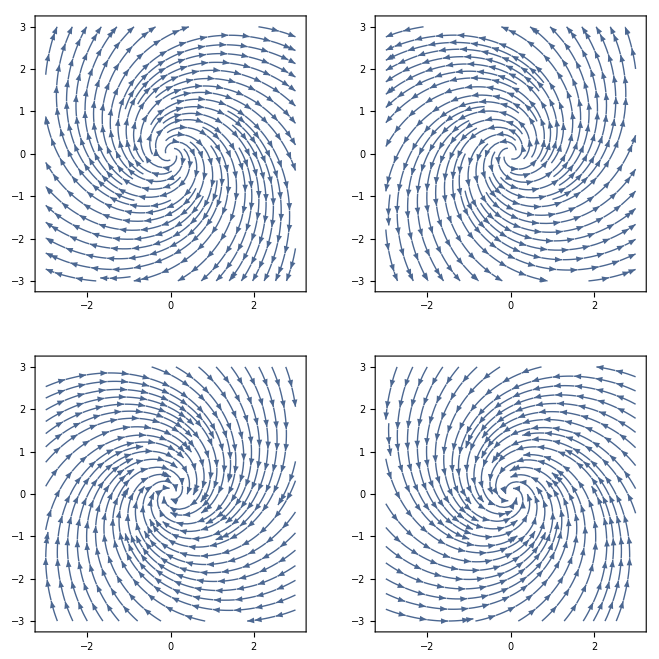

```mathematica
GraphicsGrid[{{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{1/r,-2/r},{r,θ}->{x,y}],{x,-3,3},{y,-3,3}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{1/r,2/r},{r,θ}->{x,y}],{x,-3,3},{y,-3,3}]},{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-1/r,-2/r},{r,θ}->{x,y}],{x,-3,3},{y,-3,3}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-1/r,2/r},{r,θ}->{x,y}],{x,-3,3},{y,-3,3}]}}]
```

## Acceleration field (Lagrange)

```mathematica
a:=a;
D[Sqrt[2*a*t],t]
D[Sqrt[2*a*t],t,t]
```

a/(√2 √(a t))

-a^2/(2 √2 (a t)^(3/2))

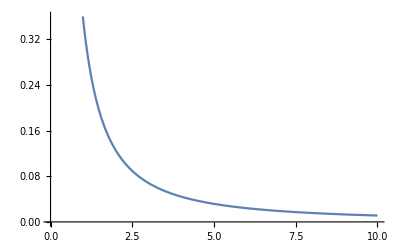

```mathematica
a=1;Plot[a^2/(2 √2 (a t)^(3/2)),{t,0,10}]
```